```mathematica
Clear["Global`*"]
K1=-7;
D1=-1.42;
K2=-1.5;
D2=-0.56;
K3=0.04;
D3=0.002;
m=0.086;
g=9.81;
J=1/12 m(0.02^2+0.035^2);
L=0.035;
(*u1max=1.224;
u2max=0.08925L;*)
Fmax=0.612;
scale=4050;
K1=-7;

(*Change between original and new controller*)
D1=-1.42;
K2=-1.5;(*Original:1.5, New:7*)
D2=-1.95;(*Original:1.95, New:3*)
(*Change between original and new controller*)

K3=.04;
D3=.002;
ωmax=19200/60*2π;
ωmin=10000/60*2π;
u11=m g+K1 (y[t]-yp[t])+D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
u21=K3(ϕdes-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω11=(u11+2 u21/L)/2 scale;
ω21=(u11-2 u21/L)/2 scale;
ω1=Max[Min[ω11,ωmax],ωmin];
ω2=Max[Min[ω21,ωmax],ωmin];
F1=lift[ω1,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]];
F2=lift[ω2,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]];
u1=F1+F2;
u2=L/2(F1-F2);

eqs={x''[t]==(u1 Sin[ϕ[t]])/m,y''[t]==-g+(u1 Cos[ϕ[t]])/m,ϕ''[t]==u2/J};
```

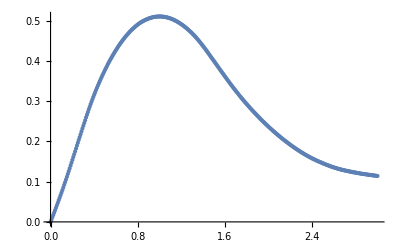

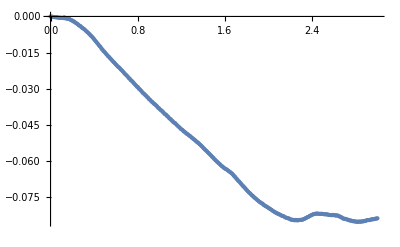

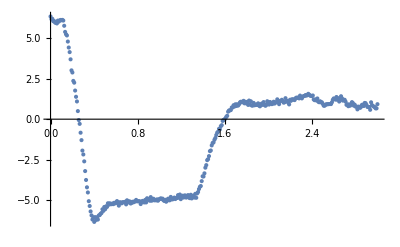

```mathematica
dir=NotebookDirectory[];
angbeg=Map[{#[[1]],-#[[2]]}&,Import[FileNameJoin[{dir,"angle_beg.csv"}]]];
horizbeg=Map[{#[[1]],-#[[2]]/1000}&,Import[FileNameJoin[{dir,"horiz_beg.csv"}]]];
vertbeg=Map[{#[[1]],-#[[2]]/1000}&,Import[FileNameJoin[{dir,"vert_beg.csv"}]]];
angmid=Map[{#[[1]]-10.525,-#[[2]]}&,Import[FileNameJoin[{dir,"angle_mid.csv"}]]];
horizmid=Map[{#[[1]]-10.525,-#[[2]]/1000+0.417149665978293}&,Import[FileNameJoin[{dir,"horiz_mid.csv"}]]];
vertmid=Map[{#[[1]]-10.525,-#[[2]]/1000-0.010586503023018601}&,Import[FileNameJoin[{dir,"vert_mid.csv"}]]];
ListPlot[horizbeg]
ListPlot[vertbeg]
ListPlot[angbeg,PlotRange->All]
```

Angle error:

```mathematica
N@ArcTan[(e*35/40)/90]*180/π/.e->4
```

2.22705

## Beginning

```mathematica
ϕdes=(Interpolation[angbeg][t]-0)*π/180;
ϕdes=Piecewise[{{0.08,(t<0.15)},{-0.14,t>0.26&&t<0.43},{-0.118,t>0.43&&t<1},{-0.105,t>1&&t<1.35},{-0.36+0.25t,t>1.35&&t<1.5},{0.028,t>1.5}}];
yp[t_]:=Piecewise[{{Interpolation[vertbeg][t],t>0.0}}];
T=3;
lift[ω_,vx_,vy_]:=1.5042947579635582*^-7 ω^2;
lift[ω_,vx_,vy_]:=-2*(0.0005917217101953038 vx^2-0.00002557102446913359 vx^4-0.0009764562665337519 vy-0.00013859859899200091 vx^2 vy+0.00004560884655456854 vy^3-7.893807214858706*^-8 ω^2);
solorig=NDSolve[eqs&&x[0]==0&&y[0]==0&&ϕ[0]==(ϕdes/.t->0)&&x'[0]==0.7&&y'[0]==0&&ϕ'[0]==0,{x[t],y[t],ϕ[t]},{t,0,T}][[1]]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}

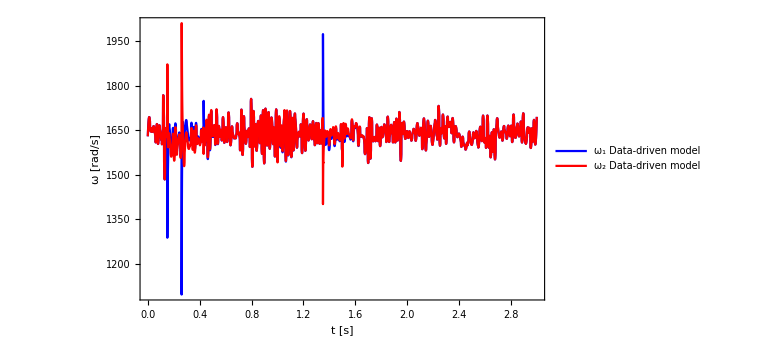

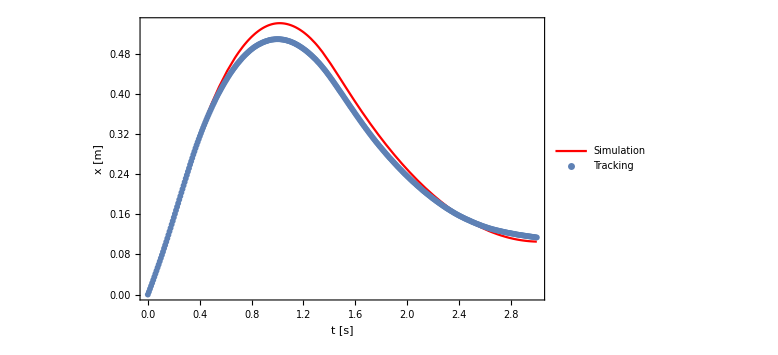

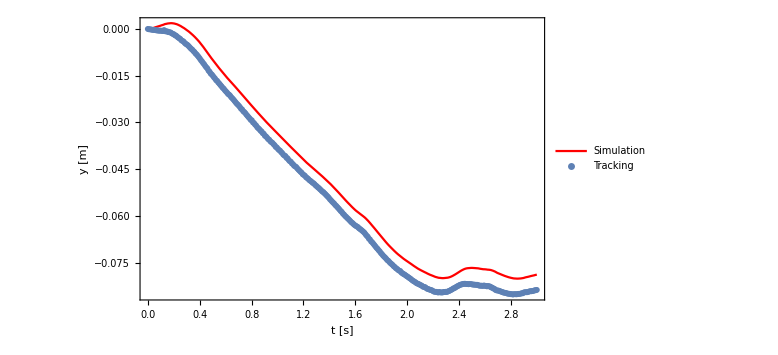

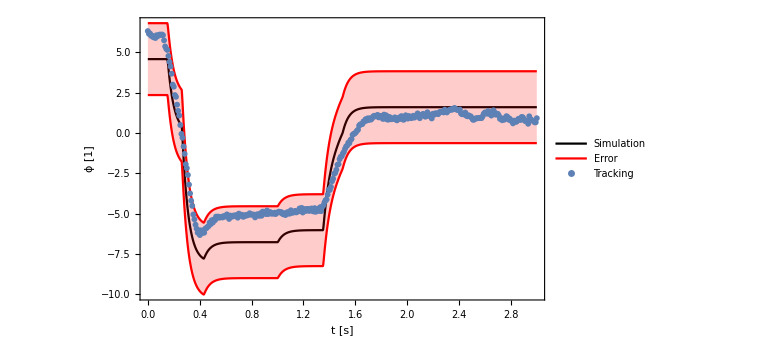

```mathematica
fontsize=20;
ctr1=u1/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ctr2=u2/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ctrph=ϕdes/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ω1vorig=ω1/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ω2vorig=ω2/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
Plot[{ω1vorig,ω2vorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle-> {Black,FontSize->36,FontFamily->"Times"},PlotLegends->Placed[{"ω_1 Data-driven model","ω_2 Data-driven model"},Below],ImageSize->Large,PlotStyle->{{Blue},{Red}},Exclusions->None]
horizplot1=Plot[{x[t]/.solorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"},ImageSize->Large,PlotStyle->{{Thick,Red}},PlotLegends->{"Simulation"}];
horizplot2=ListPlot[horizbeg,PlotLegends->{"  Tracking"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
horizplot=Show[{horizplot1,horizplot2}]
vertplot1=Plot[{y[t]/.solorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"},ImageSize->Large,PlotLegends->{"Simulation"},PlotStyle->{Thick,Red}];
vertplot2=ListPlot[vertbeg,PlotLegends->{"  Tracking"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
vertplot=Show[vertplot1,vertplot2]
angplot1=Plot[{ϕ[t]*180/π/.solorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [1]"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"},ImageSize->Large,PlotLegends->{"Simulation"},PlotStyle->{Black,Thick}];
angplot2=ListPlot[angbeg,PlotLegends->{"  Tracking"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
angplot3=Plot[{(ϕ[t]*180/π/.solorig)+2.227,(ϕ[t]*180/π/.solorig)-2.227},{t,0,T},PlotStyle->Red,Filling->{1->{2}},PlotLegends->{"Error"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
angplot=Show[angplot1,angplot3,angplot2]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_horiz1.png"}],horizplot,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_vert1.png"}],vertplot,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_ang1.png"}],angplot,ImageResolution->500];
```

## Mid

```mathematica
ϕdesintpd=(Interpolation[angmid][t]-0)*π/180;
ϕdes=Piecewise[{{ϕdesintpd-0.02,(t<0.6)},{-0.14,t>0.65&&t<0.8},{ϕdesintpd-0.02,t>0.8&&t<1.43},{0.0,t>1.43&&t<1.7},{ϕdesintpd-0.01,t>1.7&&t<2},{ϕdesintpd-0.008,t>2&&t<4},{0,t>4&&t<5.5},{ϕdesintpd,t>5.8&&t<6.5},{ϕdesintpd+0.01,t>6.5&&t<7.05},{0.13,t>7.1&&t<7.3},{ϕdesintpd,t>7.3}}];
yp[t_]:=Interpolation[vertmid][t];
T=8.28;
lift[ω_,vx_,vy_]:=-2*(0.0005917217101953038 vx^2-0.00002557102446913359 vx^4-0.0009764562665337519 vy-0.00013859859899200091 vx^2 vy+0.00004560884655456854 vy^3-7.893807214858706*^-8 ω^2);
solorig=NDSolve[eqs&&x[0]==0&&y[0]==0&&ϕ[0]==(ϕdes/.t->0)&&x'[0]==0.353&&y'[0]==0&&ϕ'[0]==0,{x[t],y[t],ϕ[t]},{t,0,T}][[1]]
```

{x[t]→InterpolatingFunction[{{0., 8.28}}, <>][t],y[t]→InterpolatingFunction[{{0., 8.28}}, <>][t],ϕ[t]→InterpolatingFunction[{{0., 8.28}}, <>][t]}

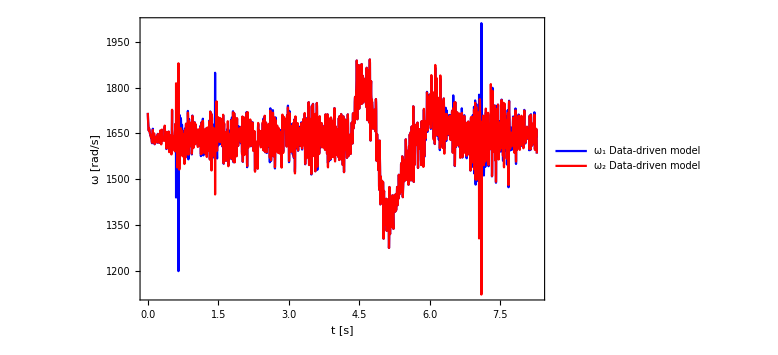

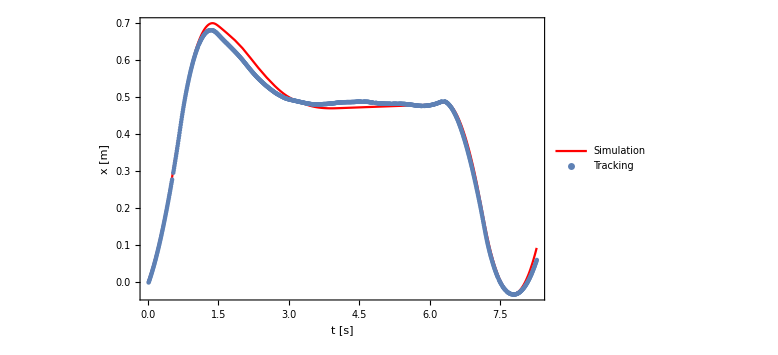

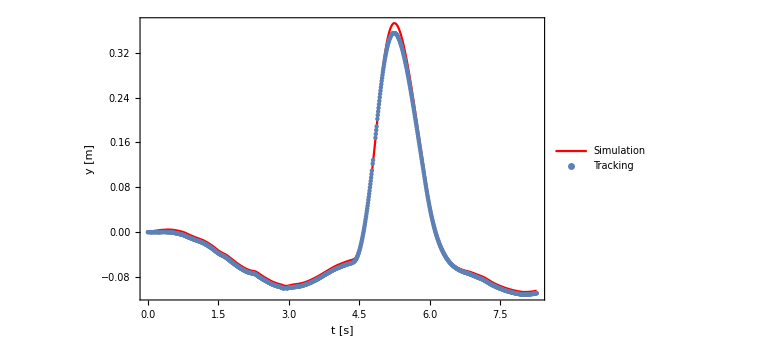

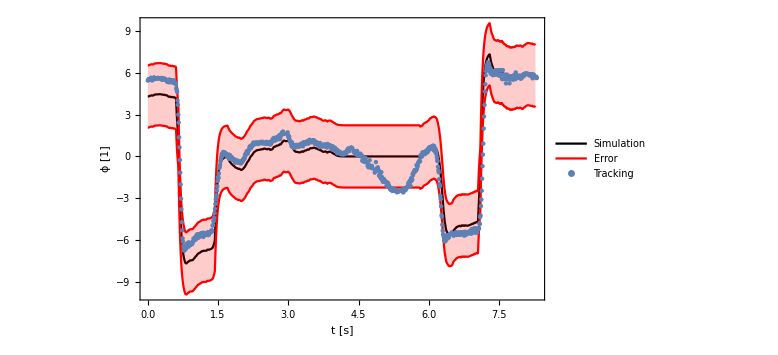

```mathematica
ctr1=u1/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ctr2=u2/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ctrph=ϕdes/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ω1vorig=ω1/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
ω2vorig=ω2/.Flatten[{solorig,D[solorig,t],D[D[solorig,t],t]}];
Plot[{ω1vorig,ω2vorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle-> {Black,FontSize->36,FontFamily->"Times"},PlotLegends->Placed[{"ω_1 Data-driven model","ω_2 Data-driven model"},Below],ImageSize->Large,PlotStyle->{{Blue},{Red}},Exclusions->None]
horizplot1=Plot[{x[t]/.solorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"},ImageSize->Large,PlotStyle->{{Thick,Red}},PlotLegends->{"Simulation"}];
horizplot2=ListPlot[horizmid,PlotLegends->{"  Tracking"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
horizplot=Show[{horizplot1,horizplot2}]
vertplot1=Plot[{y[t]/.solorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"},ImageSize->Large,PlotLegends->{"Simulation"},PlotStyle->{Thick,Red}];
vertplot2=ListPlot[vertmid,PlotLegends->{"  Tracking"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
vertplot=Show[vertplot1,vertplot2]
angplot1=Plot[{ϕ[t]*180/π/.solorig},{t,0,T},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [1]"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"},ImageSize->Large,PlotLegends->{"Simulation"},PlotStyle->{Black,Thick}];
angplot2=ListPlot[angmid,PlotLegends->{"  Tracking"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
angplot3=Plot[{(ϕ[t]*180/π/.solorig)+2.227,(ϕ[t]*180/π/.solorig)-2.227},{t,0,T},PlotStyle->Red,Filling->{1->{2}},PlotLegends->{"Error"},LabelStyle-> {Black,FontSize->fontsize,FontFamily->"Times"}];
angplot=Show[angplot1,angplot3,angplot2]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_horiz2.png"}],horizplot,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_vert2.png"}],vertplot,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_ang2.png"}],angplot,ImageResolution->500];
```